# PersistentHomology

Perform persistent homology on a point cloud dataset

## Definition

```mathematica
PersistentHomologyObject /:
	MakeBoxes[pho:PersistentHomologyObject[_],StandardForm] :=
		BoxForm`ArrangeSummaryBox[
			"PersistentHomologyObject",
			pho,
			GraphPlot[Flatten[ Table[ Abs[i-j]<->i+j,{i,1,8} ,{j,1,8}]], ImageSize->32, Background->Transparent ,GraphLayout->"CircularEmbedding"],
			 {Row[{ Style[#1,RGBColor[0.43,0.43,0.43]], StringForm["``",#2  ]  } ] }    & @@@{   {"Points: ",Length[pho["Points"]]}     ,                 {"Dimensions: ",pho["Dimension"]}          },
		 {Row[{ Style[#1,RGBColor[0.43,0.43,0.43]], StringForm["``",#2  ]  } ] }    & @@@{   {"Simplex Count: ", Length[pho["Simplices"]]  },   {"Filtration Length: ",  Length[pho["FiltrationRadii"]]-1   }  ,  {"Generators: ",  Length[pho["Intervals"]]   }    },
StandardForm
		]
Options[PersistentHomology]={"Modulus"->2,"Distance"->"Maximum"};
PersistentHomologyObject[data_]["Properties"]:=SortBy[{"Properties","PropertyDescriptions","Points","Dimension","Simplices","IntervalIndices","SimplexWeights","Intervals","Barcode","FiltrationRadii","Filtration","FiltrationMeshByIndex","GeneratorHighlightMeshes","FiltrationMeshByRadius", "Generators", "GeneratorMeshes","SimplexMeshes","MaximumDistance",{"FiltrationByIndex","n"},{"FiltrationByRadius","r"} }, If[StringQ[#], StringPart[#,1], StringPart[#[[1]]  ,1] ,Infinity ]& ]
PersistentHomologyObject[data_]["PropertyDescriptions"]:=Column[#,Spacings->0.75]&@Sort[{
"Points: The original points from the data given to PersistentHomology[].",
"Dimension: The embedding dimension of the data.",
"Simplices: A list of the simplices generated. Represented as subsets of the index set of the data. Sorted by weight.",
"IntervalIndices: Pairs of simplices represented by their index in 'Simplices' that cause the birth and then death of a generator.","SimplexWeights: The weights of the simplices in 'Simplices.",
"Intervals: 'IntervalIndices' where the simplices are replaced by their weights.",
"Barcode: The barcode diagram for all the generators formed. The generator index in 'IntervalIndices' in can be found via the Tooltip[] on the diagram.",
"FiltrationRadii: The different radii at which unique complex in the filtration form.",
"Generators: The generators of homology, represented as collections of 'Simplices' indices.",
"GeneratorMeshes: The MeshRegion[] variant of 'Generators'.",
"GeneratorHighlightMeshes: A list of GeneratorMeshes highlighted in the filtration complex at which they first occur.",
"FiltrationByIndex:  Looks up all simplices in the nth complex of the filtration.",
"SimplexMeshes: The MeshRegion[] variant of 'Simplices'.",
"Filtration: A list of all the complexes in the generated filtration.",
"FiltrationMeshByIndex: The MeshRegion[] variant of 'FiltrationByIndex'.",
"FiltrationMeshByRadius: The MeshRegion[] variant of 'FiltrationByRadius'.",
"FiltrationByRadius: Looks up all simplices with weight just above radius r in the filtration."  ,
   "MaximumDistance: The largest distance considered by default in the filtration construction."}]
PersistentHomologyObject[data_]["Points"]:=data["Points"]
PersistentHomologyObject[data_]["Dimension"]:=data["Dimension"]
PersistentHomologyObject[data_]["Simplices"]:=data["Simplices"]
PersistentHomologyObject[data_]["MaximumDistance"]:=data["MaximumDistance"]
PersistentHomologyObject[data_]["IntervalIndices"]:=data["IntervalIndices"]
PersistentHomologyObject[data_]["SimplexWeights"]:=data["SimplexWeights"]
PersistentHomologyObject[data_]["Intervals"]:=data["Intervals"]

PersistentHomologyObject[data_]["Barcode"]:=NumberLinePlot[MapIndexed[  Tooltip[Interval[#1],First[#2]]&, data["Intervals"]    ],PlotStyle->Map[ColorData["BrightBands"],((Length/@(data["Simplices"]⟦#⟧ &)/@First/@data["IntervalIndices"] -1)/data["Dimension"])],PlotLegends->Placed[LineLegend[  (Through[ {#&, Thickness[0.015] &} [ #] ]&/@ColorData["BrightBands"]/@((Range[data["Dimension"]]-1)/data["Dimension"]))~Join~{Blue},Style[#,Lighter[Blue,0.4]]&/@Subscript["H",#]&/@ (Range[ data["Dimension"] ]-1) ,LegendLayout->"Column",LegendFunction->Panel]  ,{Scaled[{0.9,0.15}], Scaled[{0.9, 0.15}]}   ]  ] 

PersistentHomologyObject[data_]["FiltrationRadii"]:=data["FiltrationRadii"]
PersistentHomologyObject[data_]["FiltrationByIndex",index_]:=data["Simplices"]⟦1;;First@FirstPosition[data["SimplexWeights"] ,x_/;x>data["FiltrationRadii"]⟦ index ⟧,{Infinity},1,Heads->False ] ⟧
PersistentHomologyObject[data_]["FiltrationByRadius",radius_]:=data["Simplices"]⟦1;;First@FirstPosition[data["SimplexWeights"] ,x_/;x>radius,{Infinity},1,Heads->False ] ⟧
PersistentHomologyObject[data_]["Edges"]:=  data["Edges"]
PersistentHomologyObject[data_]["Generators"]:=  If[ ListQ[#], #,List[#] ]&@ If[ #≤ Length[data["Points"]], #,     VertexInComponent[ data["Edges" ],   #]      ] & /@First/@ data["IntervalIndices"] 

PersistentHomologyObject[data_]["SimplexMeshes"]:=MeshRegion[data["Points"] ,#]&/@Simplex/@data["Simplices"]

(pho:PersistentHomologyObject[_])["GeneratorMeshes"]:=MeshRegion[pho["Points"] ,#]&/@(Simplex/@pho["Simplices"][[#]]& /@pho["Generators"])

(pho:PersistentHomologyObject[_])["Filtration"]:=Table[pho["FiltrationByIndex",n],{n,1,Length[ pho["FiltrationRadii"]  ]-1   }] 

(pho:PersistentHomologyObject[_])["FiltrationMeshByIndex",index_]:= MeshRegion[pho["Points"] ,#]&@(Simplex/@pho["FiltrationByIndex",index])

(pho:PersistentHomologyObject[_])["FiltrationMeshByRadius",radius_]:= MeshRegion[pho["Points"] ,#]&@(Simplex/@pho["FiltrationByRadius",radius])

(pho:PersistentHomologyObject[_])["GeneratorHighlightMeshes"]:= HighlightMesh[#[[1]],#[[2]]]&/@ Transpose[ {pho["FiltrationMeshByRadius",#]&/@(pho["SimplexWeights"][[#]]&/@(First/@pho["IntervalIndices"])), pho["GeneratorMeshes"] } ]

PersistentHomology[points_,OptionsPattern[]]:=Module[
{ComputationMessages, globalworkflow,localworkflow,maxlocalworkflow,MapProgress,data,dims, coordinates,message1,message2, SWeight, MaxD  ,dist,g,maximalsimplices, allsimps,sortedpairs,simpweights,sortedsimps,sortweights, Indices,simpIndex,maximalsimplicesEmbedded,boundary,Low,lows,newboundary,i,edges, intervals, pairs, nontrivialpairs, numintervals  },


(* Progress Variables *)


ComputationMessages = { "Extracting Data","Constructing Weight Function on Simplicies","Generating Vietoris-Rips Complex", "Applying Weight Function to Simplices","Finding Unique Complexes in Filtration","Generating Boundary Matrix","Reducing Boundary Matrix","Extracting Persistence Intervals" };
globalworkflow = 0;(*workflow index to be printed *)
localworkflow=0;(*local workflow index to be used in ProgressIndicator[] *)
MapProgress = Function[ {function,arg}, MapIndexed[First[{function[#1],localworkflow++;} ]&,arg]];


(* Extract Data *)


data = points;
dims = Length[ data[[1]] ];
If[ dims == 1, data = #&@@@ data,data = data ];
coordinates = AssociationThread[ Range[Length[data] ]-> data ];

localworkflow=0;
message1 = PrintTemporary[ StringForm[ "``",ComputationMessages[[globalworkflow+1 ]]  ]  ];
message2 = PrintTemporary[ StringForm[ "`` / 8 ",globalworkflow ]  ];
maxlocalworkflow = 1;
Monitor[
(*data = #1 *)
localworkflow++;,
 ProgressIndicator[ localworkflow ,{ 0,maxlocalworkflow } ] 
];

globalworkflow++;
NotebookDelete[message1];
NotebookDelete[message2];


(* Constructing Weight Function on Simplices *)


localworkflow=0;
message1 = PrintTemporary[ StringForm[ "``",ComputationMessages[[globalworkflow+1 ]]  ]  ];
message2 = PrintTemporary[ StringForm[ "`` / 8 ",globalworkflow ]  ];
maxlocalworkflow = 1;
Monitor[
SWeight:=  Max@ DistanceMatrix[coordinates/@#]& ; (* Old Simple Definition of SWeight *)(* Goes as n^(1.5 or 2)Log[n] *)
(*PreSWeight:= If[ Length@# == 2 ,EuclideanDistance@@ # , If[ Length@#> 2, Max[ PreSWeight /@ Subsets[ #, {Length@# -1}   ] ] , 0 ] ]&*) (* Speedier Recursive Definition w/ Memory, but no coordinates *) (* Slower for large n *)
(*SWeight := PreSWeight/@ (coordinates/@#&);*) (* Precomposing to acquire coordinate *)

MaxD = SWeight@Range@Length@data; 
localworkflow++;,
 ProgressIndicator[ localworkflow ,{ 0,maxlocalworkflow } ] 
];

globalworkflow++;
NotebookDelete[message1];
NotebookDelete[message2];

(* Generating Vietoris-Rips Complex *)


localworkflow=0;
message1 = PrintTemporary[ StringForm[ "``",ComputationMessages[[globalworkflow+1 ]]  ]  ];
message2 = PrintTemporary[ StringForm[ "`` / 8 ",globalworkflow ]  ];

dist = If[ OptionValue["Distance"] == "Maximum", MaxD, OptionValue[   "Distance"     ] ];

Monitor[
g =IndexGraph@ NearestNeighborGraph[data,{All,dist}];(* 1-Skeleton Generation *)
(*GWeighted = Graph[ g, EdgeWeight-> norm@@@ EdgeList[G] ]; (* Weighted Graph Variant *)  *)
maximalsimplices = FindClique[g,Infinity,All] ;(* Find the Largest Simplicies *) ;
allsimps = Rest@Union@Flatten[      MapProgress[Subsets[#,dims+1]&,maximalsimplices],1]; (*Select dims-Simplicies *)
maxlocalworkflow = Length[allsimps];
(*mesh = MeshRegion[data,MapProgress[Simplex,allsimps ]];*)(* Generate Mesh/Simplex Object *)
,
 ProgressIndicator[ localworkflow ,{ 0,maxlocalworkflow } ] 
];

globalworkflow++;
NotebookDelete[message1];
NotebookDelete[message2];

(* Applying Weight Function to Simplices and Sorting by Weight *)


localworkflow=0;
message1 = PrintTemporary[ StringForm[ "``",ComputationMessages[[globalworkflow+1 ]]  ]  ];
message2 = PrintTemporary[ StringForm[ "`` / 8 ",globalworkflow ]  ];
maxlocalworkflow =Length[allsimps];

Monitor[ 
simpweights = MapProgress[SWeight,allsimps];(*Slow*)
sortedpairs = SortBy[#,Last]&@  Transpose[ {allsimps,simpweights} ];
{sortedsimps,sortweights} = Transpose[sortedpairs]; ,
 ProgressIndicator[ localworkflow ,{ 0,maxlocalworkflow } ]
 ];

globalworkflow++;
NotebookDelete[message1];
NotebookDelete[message2];

(* Finding Unique Complexes in Rips Filtration *)


localworkflow=0;
message1 = PrintTemporary[ StringForm[ "``",ComputationMessages[[globalworkflow+1 ]]  ]  ];
message2 = PrintTemporary[ StringForm[ "`` / 8 ",globalworkflow ]  ];
maxlocalworkflow =Length[allsimps];

 Monitor[ 
Indices = Accumulate@DeleteDuplicates@Differences@sortweights;,
 ProgressIndicator[ localworkflow ,{ 0,maxlocalworkflow } ] 
];

globalworkflow++;
NotebookDelete[message1];
NotebookDelete[message2];

(* Generating Boundary Matrix *)

localworkflow=0;
message1 = PrintTemporary[ StringForm[ "``",ComputationMessages[[globalworkflow+1 ]]  ]  ];
message2 = PrintTemporary[ StringForm[ "`` / 8 ",globalworkflow ]  ];
maxlocalworkflow =Length[allsimps];

Monitor[
simpIndex=PositionIndex[sortedsimps][[All,1]];
maximalsimplicesEmbedded=DeleteDuplicates[Catenate[If[Length[#]<dims+1,{#},Subsets[#,{dims+1}]]&/@maximalsimplices]];
boundary=SparseArray[
Reap[
Function[clique,
Nest[
DeleteDuplicates@*Catenate@*Map[localworkflow++;With[{smaller=Table[Delete[#,i],{i,Length[#]}]},Function[s,Sow[{simpIndex[s],simpIndex[#]}]]/@smaller;smaller]&],
{clique},
Length[clique]-1]
]/@maximalsimplicesEmbedded
][[2,1]]->1,
{Length[sortedsimps],Length[sortedsimps]}
],
 ProgressIndicator[ localworkflow,{ 0,maxlocalworkflow } ] 
];

globalworkflow++;
NotebookDelete[message1];
NotebookDelete[message2];


(* Reducing Boundary Matrix (Main PH Algorithm) *)


localworkflow=0;
maxlocalworkflow  = Length[allsimps];
message1 = PrintTemporary[ StringForm[ "``",ComputationMessages[[globalworkflow+1 ]]  ]  ];
message2 = PrintTemporary[ StringForm[ "`` / 8 ",globalworkflow ]  ];

Low[mat_, column_Integer]:= Length[mat]-First[FirstPosition[Normal@Reverse@mat[[All,column]],Except[0],{-Infinity},{1},Heads->False]]+1;
lows=Low[boundary,#]&/@Range[Length[boundary[[1]]]];
newboundary=boundary;
(*ProgressIndicator[ localworkflow,{0,maxlocalworkflow }  ]    ;*)
Monitor[
edges=Block[{j},
Reap[
Do[
While[j=First@FirstPosition[Take[lows,i-1],lows[[i]],{Missing[]},{1},Heads->False];!MissingQ[j]&&IntegerQ[lows[[j]]],
newboundary[[All,i]]=Mod[newboundary[[All,i]]+newboundary[[All,j]],OptionValue["Modulus"]];
lows[[i]]=Low[newboundary,i];lows[[j]]=Low[newboundary,j];
Sow[j->i]
];localworkflow++;,
{i,1,Length[newboundary]}]
][[2,1]]
];,
ProgressIndicator[ localworkflow, {0, maxlocalworkflow} ]
];


globalworkflow++;
NotebookDelete[message1];
NotebookDelete[message2];

(* Extracting Persistence Intervals (Birth,Death) *)


localworkflow=0;
message1 = PrintTemporary[ StringForm[ "``",ComputationMessages[[globalworkflow+1 ]]  ]  ];
message2 = PrintTemporary[ StringForm[ "`` / 8 ",globalworkflow ]  ];
Monitor[
intervals=MapIndexed[{#1,First[#2]}&,lows];
pairs=Select[intervals,FreeQ[Infinity]     ]; (* need to keep intervals that last forever, i.e. only paired with infinity, at least for Subscript[H, 0] *)
nontrivialpairs = Select[ pairs, Subtract@@(Chop@sortweights[[#]]&/@# &   @#)≠ 0 &   ];
maxlocalworkflow  = Length[nontrivialpairs];
numintervals=MapProgress[sortweights[[#]]&,nontrivialpairs];
NumberLinePlot[MapIndexed[  Tooltip[Interval[#1],First[#2]]&,numintervals]];
, ProgressIndicator[ localworkflow,{0,maxlocalworkflow }   ]
];

globalworkflow++;
NotebookDelete[message1];
NotebookDelete[message2];

(*Sum[Sum[  Sum[ (Binomial[ 450,  a] Binomial[ 450, b] Binomial[ 450,12- c] Binomial[ 450, 0])/Binomial[ 1800, 12],{a,0,c-b}],{ b, 0, c}],{ c,0,12} ]*)

PersistentHomologyObject[<|
"Points"->data,
"Dimension"-> dims,
"MaximumDistance"->MaxD,
"Simplices"->sortedsimps,
"SimplexWeights"->sortweights,
"IntervalIndices"->nontrivialpairs,
"Intervals"-> numintervals,
"FiltrationRadii"-> Indices,
"Edges"-> edges



|>]
]
```

## Documentation

### Usage

PersistentHomology[{e_1,e_2,…}]

performs persistent homology on the e_i and returns a PersistentHomologyObject that can be queried for results.

PersistentHomology[{e_1,e_2,…},"Modulus"→p]

performs persistent homology over the coefficient field ℤ_p.

### Details & Options

PersistentHomology works for any dataset where the e_i are numerical lists of the same length.

The following options can be given:

"Distance" | "Maximal" | the maximal distance scale to perform homology
"Modulus" | 2 | the characteristic of the coefficient field used

## Examples

### Basic Examples

Perform persistent homology on random data:

```mathematica
SeedRandom[314];data = RandomReal[{0,1},{10,3} ];
ph=PersistentHomology[data]
```

PersistentHomologyObject[…]

Query the output for the barcode:

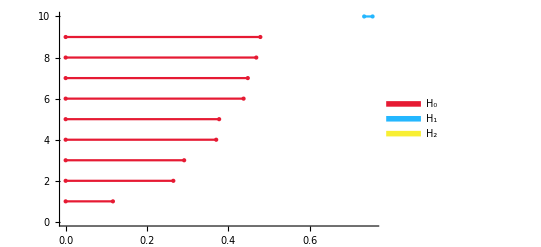

```mathematica
ph["Barcode"]
```

Visualize the MeshRegion for the H_1 generator found:

```mathematica
ph["GeneratorMeshes"][[10]]
```

-Graphics3D-

### Scope

#### Dimensionality

PersistentHomology can be performed for data of any dimension:

```mathematica
data=RandomReal[{0,1},{10,42}];
```

```mathematica
PersistentHomology[data]
```

PersistentHomologyObject[…]

Evaluate the persistent homology of data with dimension 1000:

```mathematica
data=RandomReal[{0,1},{10,1000}];
```

```mathematica
PersistentHomology[data]
```

PersistentHomologyObject[…]

### Options

#### Distance

The maximum distance used in computations can be specified:

```mathematica
data=RandomReal[{0,1},{10,3}];
```

```mathematica
PersistentHomology[data,"Distance"->0.75]
```

PersistentHomologyObject[…]

This will sometimes speed up computation times:

```mathematica
AbsoluteTiming[PersistentHomology[data,"Distance"->0.75]]
```

{7.64044,PersistentHomologyObject[…]}

```mathematica
AbsoluteTiming[PersistentHomology[data]]
```

{7.52512,PersistentHomologyObject[…]}

#### Modulus

The finite field chosen for computations can be specified:

```mathematica
data=RandomReal[{0,1},{10,3}];
```

```mathematica
PersistentHomology[data,"Modulus"->7]
```

PersistentHomologyObject[<|Points -> {{0.540558, 0.208324, 0.0814161}, {0.00129297, 0.446641, 0.894455}, {0.164448, 0.609031, 0.0627587}, {0.115234, 0.441508, 0.799684}, {0.41501, 0.426921, 0.87408}, {0.471, 0.415582, 0.295995}, {0.457074, 0.890579, 0.952611}, {0.552771, 0.653242, 0.356828}, {0.279893, 0.462175, 0.945655}, {0.990844, 0.0672289, 0.938108}}, <<7>>, Edges -> <<1>>|>]

### Properties and Relations

PersistentHomology is invariant under isometries:

```mathematica
data=SpherePoints[10];
```

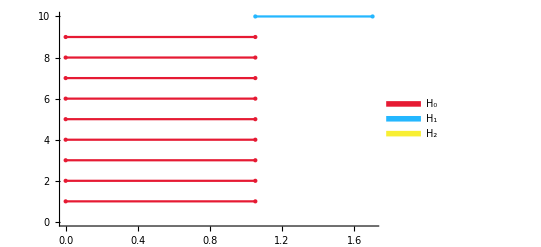

```mathematica
PersistentHomology[data]["Barcode"]
```

```mathematica
PersistentHomology[({0,0,1}+#1&)/@SpherePoints[10]]["Barcode"]
```

-Graphics-

```mathematica
PersistentHomology[RotationTransform[π/4,{1,1,1}][data]]["Barcode"]
```

-Graphics-

### Possible Issues

PersistentHomology computation times grow quickly in the number of data points:

```mathematica
data=RandomReal[{0,1},{20,3}];
AbsoluteTiming[PersistentHomology[data⟦1;;5⟧]]
```

{6.95572,PersistentHomologyObject[…]}

```mathematica
AbsoluteTiming[PersistentHomology[data⟦1;;10⟧]]
```

{7.33262,PersistentHomologyObject[…]}

```mathematica
AbsoluteTiming[PersistentHomology[data⟦1;;15⟧]]
```

{22.7267,PersistentHomologyObject[<|Points -> {{0.407456, 0.324138, 0.252778}, {0.966994, 0.613372, 0.815813}, {0.336938, 0.54071, 0.372096}, {0.028556, 0.764784, 0.736238}, {0.736004, 0.350236, 0.99665}, {0.815259, 0.247619, 0.242471}, {0.168575, 0.126054, 0.407273}, <<5>>, {0.0485355, 0.101531, 0.487586}, {0.164593, 0.391053, 0.7659}, {0.0732095, 0.775192, 0.537681}}, <<8>>|>]}

```mathematica
AbsoluteTiming[PersistentHomology[data⟦1;;20⟧]]
```

{225.966,PersistentHomologyObject[<|Points -> {{0.407456, 0.324138, 0.252778}, {0.966994, 0.613372, 0.815813}, {0.336938, 0.54071, 0.372096}, {0.028556, 0.764784, 0.736238}, {0.736004, 0.350236, 0.99665}, {0.815259, 0.247619, 0.242471}, {0.168575, 0.126054, 0.407273}, <<10>>, {0.248729, 0.295658, 0.758131}, {0.398079, 0.758276, 0.725927}, {0.348824, 0.452581, 0.362966}}, <<8>>|>]}

### Neat Examples

Draw some data in ℝ^2 and perform PersistentHomology on it:

```mathematica
DynamicModule[{data={},phom=Graphics[{}]},
Column[{
Button["Compute",phom=PersistentHomology[data]["Barcode"]],
Row@{ClickPane[Framed@Dynamic[ListPlot[data,PlotRange->{ {-1,1},{-1,1} },PlotStyle->PointSize[Large],ImageSize->250,PlotLabel->Length[data]],],AppendTo[data,#]&],Dynamic[Show[phom,ImageSize->250]]}
},Alignment->Left
]]
```

-Graphics-

## Source & Additional Information

### Contributed By

Andrew Ortegaray

### Keywords

Persistent Homology

Algebraic Topology

Topological Data Analysis

Algebra

Topology

Mathematics

barcodes

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

NearestNeighborGraph

DistanceMatrix

DimensionReduce

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Ghrist, R. "Barcodes: the persistent topology of data." Bulletin of the American Mathematical Society, vol. 45, no. 1, 61–75, 2008.

Otter, N. et al., "A roadmap for the computation of persistent homology." EPJ Data Science, vol. 6, no. 1, pg. 17, 2017.

Zomorodian, A., Carlsson, G., "Computing persistent homology." Discrete & Computational Geometry, vol. 33, no. 2, 249–274, 2005.

Zomorodian, A., "Fast construction of the Vietoris-Rips complex." Computers & Graphics, vol. 34, no. 3, 263–271, 2010.

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.